```mathematica
(* ============================================================ *)
(* PAIRFIT - STRUCTURAL VERSION: MeV FIT, MeV EXPORT           *)
(* ============================================================ *)
(* Evaluate after:                                                *)
(*   Get["Intro_DualMass_VacuumFitted_Cugnon_v2.wl"]       *)
(*                                                                *)
(* Purpose:                                                       *)
(*   1. Fit the p pi+ invariant-mass distribution in MeV.         *)
(*   2. Use the same physical fit strategy as the working GeV      *)
(*      PairFit, but with a MeV input data file.                   *)
(*   3. Register fitted parameters directly in the MeV convention  *)
(*      expected by the main Delta analysis.                       *)
(*                                                                *)
(* Unit convention:                                                *)
(*   - Input file is expected to be already converted to MeV:       *)
(*       M_low, M_high, M_center        in MeV                     *)
(*       dN/dM, errors                  in 1/MeV                   *)
(*   - Fit windows, plots, models and exported parameters are MeV.  *)
(*   - No hidden GeV <-> MeV conversion is performed here.          *)
(*                                                                *)
(* Numerical policy:                                               *)
(*   - No AccuracyGoal.                                            *)
(*   - No PrecisionGoal.                                           *)
(*   - Integrals use only WorkingPrecision and MaxRecursion.        *)
(* ============================================================ *)

If[$InputFileName =!= "",
  SetDirectory[DirectoryName[$InputFileName]],
  If[ValueQ[NotebookDirectory[]], SetDirectory[NotebookDirectory[]]]
];

(* This file intentionally does not redefine rhoBW, rhoCugnon or
   rhoPhaseShift from Intro.  It only calibrates the mass-shape
   parameters from the p pi+ pair spectrum and sends them to Intro
   through registerFittedMassParameters. *)
```

```mathematica
(* ============================================================ *)
(* 1. USER SETTINGS                                              *)
(* ============================================================ *)

pairFitDataFileCandidates = {
  "DeltaMass_piPlus_p_0_10_Fig2_dNdM_MeV.txt",
  "DeltaMass_piPlus_p_0_10_Fig2_dNdM.txt",
  "hades_delta_mass_integrated_with_uncertainties_MeV.txt",
  "PairMassData_MeV.txt"
};

(* Same windows as in the old comparison notebook, but in MeV. *)
pairDisplayMassWindowMeV = {1080., 1500.};
pairFitMassWindowMeV = {1100., 1400.};
pairNormalizationWindowMeV = pairFitMassWindowMeV;

(* Allowed values: "Statistical", "Systematic", "Total". *)
pairErrorMode = "Total";

pairOptimizationWorkingPrecision = MachinePrecision;
pairOptimizationMaxIterations = 5000;

(* Local integration settings for PairFit.  Do not depend on a symbolic
   nIntegrateMethod variable from another notebook/subkernel.  The explicit
   method list avoids NIntegrate::bdmtd when definitions are distributed to
   parallel kernels. *)
pairNIntegrateMethod = {"GlobalAdaptive", "SymbolicProcessing" -> 0};
pairWorkingPrecision = If[ValueQ[wpInt] && NumericQ[wpInt], wpInt, MachinePrecision];
pairMaxRecursion = If[ValueQ[maxRecInt] && IntegerQ[maxRecInt], maxRecInt, 20];

(* Fit the three independent model families in parallel.  The chi2 evaluator itself
   is also written so that the normalization integral is computed once per parameter
   vector, not once per fitted data point. *)
pairUseParallelModelFits = True;
pairUseParallelCurveSampling = False;
(* Curve sampling is intentionally sequential.  It is cheap compared with the fits and avoids stale PhaseShift definitions/parameters on subkernels. *)

pairPositiveEpsilon = 10^-12;
pairPhaseDerivativeStepMeV = 10^-3;

(* In MeV convention the Lo expansion uses q in MeV:
     Pi[q] = c1 q^2 + c2 q^4
   Therefore c1 has units MeV^-2 and c2 has units MeV^-4.
   For numerical stability the optimizer uses scaled variables:
     u1 = c1 / 10^-6
     u2 = c2 / 10^-12
   The physical parameters are always c1 [MeV^-2] and c2 [MeV^-4].  The optimizer only uses internal dimensionless variables u1,u2 to avoid searching directly over tiny numbers. *)
pairC1Scale = 10^-6;
pairC2Scale = 10^-12;

(* alpha0 is dimensionless.  In the Pok Man Lo / PhaseShift
   parameterization it should not be allowed to collapse to an
   almost zero value simply to mimic a threshold artifact.  The
   vacuum value is O(10), alpha0LoVacuum ~ 45.37, so the fit
   range is kept on the same physical scale. *)
pairPhaseShiftM0Bounds = {1150., 1300.};
pairPhaseShiftAlpha0Bounds = {5., 500.};

(* Initial values are taken from the vacuum parameter set defined in Intro.
   This keeps PairFit anchored to the same physics conventions as the main
   analysis.  Only if Intro did not define vacuumMassParameters do we fall
   back to explicit vacuum-like numbers. *)
pairVacuumMassParametersForFit = If[
  ValueQ[vacuumMassParameters] && AssociationQ[vacuumMassParameters],
  vacuumMassParameters,
  <|
    "BreitWigner" -> <|"M0" -> mD, "Gamma0" -> Γ|>,
    "Cugnon" -> <|"M0" -> mD, "Gamma0" -> Γ, "mu" -> If[ValueQ[muCugnon], muCugnon, 180.]|>,
    "PhaseShift" -> <|"M0" -> mD, "alpha0" -> alpha0PS, "c1" -> c1PS, "c2" -> c2PS|>
  |>
];

pairInitialParametersMeV = <|
  "BreitWigner" -> <|
    "M0" -> N @ pairVacuumMassParametersForFit["BreitWigner"]["M0"],
    "Gamma0" -> N @ pairVacuumMassParametersForFit["BreitWigner"]["Gamma0"]
  |>,
  "Cugnon" -> <|
    "M0" -> N @ pairVacuumMassParametersForFit["Cugnon"]["M0"],
    "Gamma0" -> N @ pairVacuumMassParametersForFit["Cugnon"]["Gamma0"],
    "mu" -> N @ pairVacuumMassParametersForFit["Cugnon"]["mu"]
  |>,
  "PhaseShift" -> <|
    "M0" -> N @ pairVacuumMassParametersForFit["PhaseShift"]["M0"],
    "alpha0" -> N @ pairVacuumMassParametersForFit["PhaseShift"]["alpha0"],
    "c1u" -> N @ (pairVacuumMassParametersForFit["PhaseShift"]["c1"]/pairC1Scale),
    "c2u" -> N @ (pairVacuumMassParametersForFit["PhaseShift"]["c2"]/pairC2Scale)
  |>
|>;

pairThresholdMeV = N[mp + mpi];

pairParameterBoundsMeV = <|
  "BreitWigner" -> <|
    "M0" -> {pairThresholdMeV + 10^-6, 1500.},
    "Gamma0" -> {10^-6, 1000.}
  |>,
  "Cugnon" -> <|
    "M0" -> {pairThresholdMeV + 10^-6, 1500.},
    "Gamma0" -> {10^-6, 1000.},
    "mu" -> {10^-6, 1000.}
  |>,
  "PhaseShift" -> <|
    (* Keep the Lo pole away from the N+pi threshold.
       If M0 is allowed to sit at threshold, the numerical derivative of
       the phase shift develops a very narrow spike and the normalized PDF
       becomes many orders of magnitude larger than BW/Cugnon in the display
       window.  This was the reason the PhaseShift curve was invisible in
       the combined plot. *)
    "M0" -> pairPhaseShiftM0Bounds,
    "alpha0" -> pairPhaseShiftAlpha0Bounds,
    (* u1 and u2 are internal dimensionless optimizer variables.
       They correspond to c1 = u1*10^-6 MeV^-2 and
       c2 = u2*10^-12 MeV^-4.  They are not exported as physical fit parameters. *)
    "c1u" -> {1., 500.},
    "c2u" -> {1., 1000.}
  |>
|>;
```

```mathematica
(* ============================================================ *)
(* 2. IMPORT DATA IN MeV                                         *)
(* ============================================================ *)

pairFitDataFile = SelectFirst[pairFitDataFileCandidates, FileExistsQ, Missing["NotFound"]];
If[MissingQ[pairFitDataFile],
  Print["ERROR: PairFit data file not found. Expected one of: ", pairFitDataFileCandidates];
  Abort[];
];

pairRawImport = Import[pairFitDataFile, "Table"];

(* Expected MeV layout:
     1 bin
     2 M_low_MeV_c2
     3 M_high_MeV_c2
     4 M_center_MeV_c2
     5 dN_dM      [1/MeV]
     6 stat_err   [1/MeV]
     7 syst_err   [1/MeV]
     8 total_err  [1/MeV]

   This is the same column structure as the HADES GeV file, but
   already converted to MeV.  We do not multiply or divide anything
   by 1000 here. *)
pairRowsMeV = Select[
  pairRawImport,
  ListQ[#] && Length[#] >= 8 && And @@ (NumericQ /@ #[[1 ;; 8]]) &
][[All, 1 ;; 8]];

If[Length[pairRowsMeV] < 5,
  Print["ERROR: too few numeric rows after import: ", Length[pairRowsMeV]];
  Abort[];
];

pairBinWidthMeV[row_List] := row[[3]] - row[[2]];
pairMassCenterMeV[row_List] := row[[4]];
pairYieldPerMeV[row_List] := row[[5]];
pairErrorPerMeV[row_List] := Switch[pairErrorMode,
  "Statistical", row[[6]],
  "Systematic", row[[7]],
  _, row[[8]]
];

pairDisplayRowsMeV = Select[pairRowsMeV, pairDisplayMassWindowMeV[[1]] <= pairMassCenterMeV[#] <= pairDisplayMassWindowMeV[[2]] &];
pairFitRowsMeV = Select[pairRowsMeV, pairFitMassWindowMeV[[1]] <= pairMassCenterMeV[#] <= pairFitMassWindowMeV[[2]] &];
pairNormRowsMeV = Select[pairRowsMeV, pairNormalizationWindowMeV[[1]] <= pairMassCenterMeV[#] <= pairNormalizationWindowMeV[[2]] &];

If[Length[pairFitRowsMeV] < 5,
  Print["ERROR: too few points in pairFitMassWindowMeV = ", pairFitMassWindowMeV];
  Print["Imported mass range [MeV] = ", {Min[pairRowsMeV[[All, 4]]], Max[pairRowsMeV[[All, 4]]] }];
  Abort[];
];

If[Length[pairNormRowsMeV] < 5,
  Print["ERROR: too few points in pairNormalizationWindowMeV = ", pairNormalizationWindowMeV];
  Abort[];
];

(* The experimental dN/dM is converted into a probability-density
   shape by dividing by the binned area in the same normalization
   window as the model PDFs.  Because dN/dM is already 1/MeV and
   the bin width is MeV, this area is dimensionless. *)
pairDataAreaMeV = Total[(pairYieldPerMeV[#]*pairBinWidthMeV[#]) & /@ pairNormRowsMeV];

If[! NumericQ[pairDataAreaMeV] || pairDataAreaMeV <= 0,
  Print["ERROR: non-positive data normalization area: ", pairDataAreaMeV];
  Abort[];
];

pairMassValsMeV = pairMassCenterMeV /@ pairFitRowsMeV;
pairYValsPDFMeV = (pairYieldPerMeV[#]/pairDataAreaMeV) & /@ pairFitRowsMeV;
pairErrorValsPDFMeV = (pairErrorPerMeV[#]/pairDataAreaMeV) & /@ pairFitRowsMeV;

pairPositiveErrors = Select[pairErrorValsPDFMeV, NumericQ[#] && # > 0 &];
If[Length[pairPositiveErrors] == 0,
  Print["ERROR: no positive errors available for weighted chi2."];
  Abort[];
];
pairErrorValsPDFMeV = pairErrorValsPDFMeV /. x_?NumericQ /; x <= 0 -> Min[pairPositiveErrors];
pairWeights = 1/pairErrorValsPDFMeV^2;
pairXYDataMeV = Transpose[{pairMassValsMeV, pairYValsPDFMeV}];

pairDisplayDataPDFMeV = ({pairMassCenterMeV[#], pairYieldPerMeV[#]/pairDataAreaMeV} &) /@ pairDisplayRowsMeV;

pairDataAssociation = <|
  "File" -> pairFitDataFile,
  "RowsMeV" -> pairRowsMeV,
  "DisplayRowsMeV" -> pairDisplayRowsMeV,
  "FitRowsMeV" -> pairFitRowsMeV,
  "NormRowsMeV" -> pairNormRowsMeV,
  "XYDataMeV" -> pairXYDataMeV,
  "DisplayDataPDFMeV" -> pairDisplayDataPDFMeV,
  "Weights" -> pairWeights,
  "ErrorsPDFMeV" -> pairErrorValsPDFMeV,
  "AreaMeV" -> pairDataAreaMeV,
  "NImportedRows" -> Length[pairRowsMeV],
  "NDisplayedPoints" -> Length[pairDisplayRowsMeV],
  "NFittedPoints" -> Length[pairFitRowsMeV],
  "FitWindowMeV" -> pairFitMassWindowMeV,
  "DisplayWindowMeV" -> pairDisplayMassWindowMeV,
  "NormalizationWindowMeV" -> pairNormalizationWindowMeV
|>;

pairImportSummaryTable = Grid[
  {
    {"Quantity", "Value"},
    {"Data file", pairFitDataFile},
    {"Imported numeric rows", Length[pairRowsMeV]},
    {"Displayed points", Length[pairDisplayRowsMeV]},
    {"Fitted points", Length[pairFitRowsMeV]},
    {"Display window [MeV]", pairDisplayMassWindowMeV},
    {"Fit window [MeV]", pairFitMassWindowMeV},
    {"PDF normalization window [MeV]", pairNormalizationWindowMeV},
    {"Data normalization area", ScientificForm[N[pairDataAreaMeV], {10, 5}]},
    {"Error mode", pairErrorMode}
  },
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairDataPreviewTable = Grid[
  Prepend[
    ({#[[1]], #[[2]], #[[3]], #[[4]], ScientificForm[#[[5]], {10, 5}], ScientificForm[#[[8]], {10, 5}]} & /@ Take[pairRowsMeV, UpTo[8]]),
    {"bin", "M_low [MeV]", "M_high [MeV]", "M_center [MeV]", "dN/dM [1/MeV]", "total err [1/MeV]"}
  ],
  Frame -> All, Background -> {LightGray, None}
];

Print["PairFit import summary:"];
Print[pairImportSummaryTable];
Print["PairFit data preview - columns actually used by this notebook:"];
Print[pairDataPreviewTable];
```

PairFit import summary:

Quantity | Value
Data file | DeltaMass_piPlus_p_0_10_Fig2_dNdM.txt
Imported numeric rows | 58
Displayed points | 40
Fitted points | 30
Display window [MeV] | {1080.,1500.}
Fit window [MeV] | {1100.,1400.}
PDF normalization window [MeV] | {1100.,1400.}
Data normalization area | 3.35989
Error mode | Total

PairFit data preview - columns actually used by this notebook:

bin | M_low [MeV] | M_high [MeV] | M_center [MeV] | dN/dM [1/MeV] | total err [1/MeV]
3 | 1087.84 | 1097.84 | 1092.84 | 8.29057×10^-3 | 1.0976×10^-3
4 | 1097.84 | 1107.84 | 1102.84 | 1.38706×10^-2 | 1.77942×10^-3
5 | 1107.84 | 1117.84 | 1112.84 | 1.71487×10^-2 | 2.14001×10^-3
6 | 1117.84 | 1127.84 | 1122.84 | 1.95205×10^-2 | 2.52734×10^-3
7 | 1127.84 | 1137.84 | 1132.84 | 2.12021×10^-2 | 2.70183×10^-3
8 | 1137.84 | 1147.84 | 1142.84 | 2.19546×10^-2 | 2.76003×10^-3
9 | 1147.84 | 1157.84 | 1152.84 | 2.21031×10^-2 | 2.76441×10^-3
10 | 1157.84 | 1167.84 | 1162.84 | 2.17573×10^-2 | 2.71749×10^-3

```mathematica
(* ============================================================ *)
(* 3. MODEL DEFINITIONS DIRECTLY IN MeV                          *)
(* ============================================================ *)

ClearAll[pairPStarMeV, pairBWRawMeV, pairCugnonRawMeV, pairPiLoMeV, pairDeltaLoMeV, pairPhaseDerivativeMeV, pairLoRawMeV];

pairPStarMeV[M_?NumericQ, m1_?NumericQ, m2_?NumericQ] := Module[{rad},
  rad = (M^2 - (m1 + m2)^2) (M^2 - (m1 - m2)^2);
  If[M <= 0 || rad <= 0, 0., Sqrt[rad]/(2 M)]
];

pairBWRawMeV[M_?NumericQ, M0_?NumericQ, Gamma0_?NumericQ] :=
  If[Gamma0 <= 0, 0., 1/((M - M0)^2 + (Gamma0/2)^2)];

pairCugnonRawMeV[M_?NumericQ, M0_?NumericQ, Gamma0_?NumericQ, mu_?NumericQ] := Module[{q},
  q = pairPStarMeV[M, mp, mpi];
  If[q <= 0 || Gamma0 <= 0 || mu <= 0,
    0.,
    (q^3/(q^3 + mu^3))*(1/(1 + 4 ((M - M0)/Gamma0)^2))
  ]
];

pairPiLoMeV[q_?NumericQ, c1_?NumericQ, c2_?NumericQ] := c1 q^2 + c2 q^4;

pairDeltaLoMeV[M_?NumericQ, M0_?NumericQ, alpha0_?NumericQ, c1u_?NumericQ, c2u_?NumericQ] := Module[
  {q, denom, x, delta, c1, c2},
  c1 = c1u*pairC1Scale;
  c2 = c2u*pairC2Scale;
  q = pairPStarMeV[M, mp, mpi];
  denom = M^2 - M0^2;
  If[M <= pairThresholdMeV || q <= 0,
    0.,
    If[Abs[denom] < 10^-6,
      Pi/2,
      x = -(2/(3 M))*(q^3/denom)*(alpha0/(1 + pairPiLoMeV[q, c1, c2]));
      delta = ArcTan[x];
      If[M > M0, delta + Pi, delta]
    ]
  ]
];

pairPhaseDerivativeMeV[f_, M_?NumericQ] :=
  (f[M + pairPhaseDerivativeStepMeV] - f[M - pairPhaseDerivativeStepMeV])/(2 pairPhaseDerivativeStepMeV);

pairLoRawMeV[M_?NumericQ, M0_?NumericQ, alpha0_?NumericQ, c1u_?NumericQ, c2u_?NumericQ] := Module[{val},
  If[M <= pairThresholdMeV,
    0.,
    val = 2 pairPhaseDerivativeMeV[Function[x, pairDeltaLoMeV[x, M0, alpha0, c1u, c2u]], M];
    If[NumericQ[val] && Chop[Im[N[val]]] == 0 && Re[N[val]] >= 0, Re[N[val]], 0.]
  ]
];

ClearAll[pairShapeNormMeV, pairPDFValueMeV, pairBWPDFMeV, pairCugnonPDFMeV, pairLoPDFMeV];

pairShapeNormMeV[shape_, params_List] := Quiet @ NIntegrate[
  Evaluate[shape[M, Sequence @@ params]],
  {M, pairNormalizationWindowMeV[[1]], pairNormalizationWindowMeV[[2]]},
  Method -> pairNIntegrateMethod,
  WorkingPrecision -> pairWorkingPrecision,
  MaxRecursion -> pairMaxRecursion
];

pairPDFValueMeV[shape_, params_List, M_?NumericQ] := Module[{norm, raw},
  norm = pairShapeNormMeV[shape, params];
  raw = shape[M, Sequence @@ params];
  If[! NumericQ[norm] || norm <= 0 || ! NumericQ[raw] || raw < 0,
    Indeterminate,
    raw/norm
  ]
];

pairBWPDFMeV[M_?NumericQ, M0_?NumericQ, Gamma0_?NumericQ] := pairPDFValueMeV[pairBWRawMeV, {M0, Gamma0}, M];
pairCugnonPDFMeV[M_?NumericQ, M0_?NumericQ, Gamma0_?NumericQ, mu_?NumericQ] := pairPDFValueMeV[pairCugnonRawMeV, {M0, Gamma0, mu}, M];
pairLoPDFMeV[M_?NumericQ, M0_?NumericQ, alpha0_?NumericQ, c1u_?NumericQ, c2u_?NumericQ] := pairPDFValueMeV[pairLoRawMeV, {M0, alpha0, c1u, c2u}, M];

pairInitialParameterTable = Grid[
  Prepend[KeyValueMap[{#1, #2} &, pairInitialParametersMeV], {"Model", "Initial parameters in MeV-fit convention"}],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];
Print["Initial parameters for MeV fit:"];
Print[pairInitialParameterTable];
```

Initial parameters for MeV fit:

Model | Initial parameters in MeV-fit convention
BreitWigner | <|M0→1232.,Gamma0→117.|>
Cugnon | <|M0→1232.,Gamma0→117.,mu→180.|>
PhaseShift | <|M0→1232.,alpha0→45.37,c1u→16.7,c2u→65.6|>

```mathematica
(* ============================================================ *)
(* 4. NUMERIC CHI2 FITS IN MeV                                   *)
(* ============================================================ *)

ClearAll[pairChi2MeV, pairObjectiveFunction, pairPValue, pairModelSpecs, pairFitModelMeV];

pairChi2MeV[rawShape_, parValues_List] := Module[{norm, rawPred, pred},
  If[! VectorQ[parValues, NumericQ], Return[10^100]];

  (* Critical speed fix:
     The older MeV version evaluated the normalized PDF at each data point, and
     each PDF call recomputed the same normalization integral.  Here the integral
     is computed once for the current parameter vector and reused for all points. *)
  norm = Quiet @ Check[pairShapeNormMeV[rawShape, parValues], $Failed];
  If[norm === $Failed || ! NumericQ[norm] || norm <= 0, Return[10^100]];

  rawPred = rawShape @@@ ({#, Sequence @@ parValues} & /@ pairMassValsMeV);
  If[! VectorQ[rawPred, NumericQ] || ! FreeQ[rawPred, Indeterminate | ComplexInfinity | DirectedInfinity[_]],
    Return[10^100]
  ];

  pred = rawPred/norm;
  If[! VectorQ[pred, NumericQ] || ! FreeQ[pred, Indeterminate | ComplexInfinity | DirectedInfinity[_]],
    10^100,
    Total[pairWeights*(pairYValsPDFMeV - pred)^2]
  ]
];

pairObjectiveFunction[model_][pars__?NumericQ] := pairChi2MeV[model, {pars}];

pairPValue[chi2_?NumericQ, ndf_Integer] := If[ndf > 0, SurvivalFunction[ChiSquareDistribution[ndf], chi2], Missing["NotAvailable"]];

pairModelSpecs = <|
  "BreitWigner" -> <|"RawFunction" -> pairBWRawMeV, "PDFFunction" -> pairBWPDFMeV, "ParameterNames" -> {"M0", "Gamma0"}|>,
  "Cugnon" -> <|"RawFunction" -> pairCugnonRawMeV, "PDFFunction" -> pairCugnonPDFMeV, "ParameterNames" -> {"M0", "Gamma0", "mu"}|>,
  "PhaseShift" -> <|"RawFunction" -> pairLoRawMeV, "PDFFunction" -> pairLoPDFMeV, "ParameterNames" -> {"M0", "alpha0", "c1u", "c2u"}|>
|>;

pairFitModelMeV[name_String] := Module[
  {spec, model, parNames, vars, init, bounds, constraints, objective, solution, bestRules, bestParams, chi2, ndf, aic, status},

  spec = pairModelSpecs[name];
  model = spec["RawFunction"];
  parNames = spec["ParameterNames"];

  vars = ToExpression["pairVar" <> name <> # & /@ parNames];
  init = N @ Lookup[pairInitialParametersMeV[name], parNames];
  bounds = Lookup[pairParameterBoundsMeV[name], parNames];

  constraints = And @@ MapThread[#2[[1]] <= #1 <= #2[[2]] &, {vars, bounds}];
  objective = pairObjectiveFunction[model] @@ vars;

  solution = Quiet @ Check[
    NMinimize[
      {objective, constraints},
      vars,
      WorkingPrecision -> pairOptimizationWorkingPrecision,
      MaxIterations -> pairOptimizationMaxIterations,
      Method -> {"NelderMead", "InitialPoints" -> {init}}
    ],
    $Failed
  ];

  If[solution === $Failed || ! ListQ[solution],
    Return[<|"Status" -> "FitFailed", "Chi2" -> Missing["FitFailed"], "NDF" -> Missing["FitFailed"],
      "Chi2NDF" -> Missing["NotAvailable"], "AIC" -> Missing["FitFailed"],
      "PValue" -> Missing["FitFailed"], "BestFitParametersMeVFit" -> Missing["FitFailed"]|>]
  ];

  bestRules = solution[[2]];
  bestParams = AssociationThread[parNames, N[vars /. bestRules]];
  chi2 = N[solution[[1]]];
  ndf = Length[pairMassValsMeV] - Length[parNames];
  aic = chi2 + 2 Length[parNames];
  status = If[NumericQ[chi2] && chi2 < 10^90, "OK", "PenaltyMinimum"];

  <|
    "Status" -> status,
    "Chi2" -> chi2,
    "NDF" -> ndf,
    "Chi2NDF" -> If[ndf > 0 && NumericQ[chi2], chi2/ndf, Missing["NotAvailable"]],
    "AIC" -> aic,
    "PValue" -> pairPValue[chi2, ndf],
    "BestFitParametersMeVFit" -> bestParams,
    "ParameterNames" -> parNames,
    "ModelFunction" -> model,
    "InitialChi2" -> pairChi2MeV[model, init]
  |>
];

pairFitResultsMeV = If[pairUseParallelModelFits,
  Quiet @ LaunchKernels[];
  DistributeDefinitions[
    pairFitModelMeV, pairChi2MeV, pairObjectiveFunction, pairPValue,
    pairModelSpecs, pairInitialParametersMeV, pairParameterBoundsMeV,
    pairMassValsMeV, pairYValsPDFMeV, pairWeights,
    pairShapeNormMeV, pairPStarMeV, pairBWRawMeV, pairCugnonRawMeV,
    pairPiLoMeV, pairDeltaLoMeV, pairPhaseDerivativeMeV, pairLoRawMeV,
    pairThresholdMeV, pairPhaseShiftM0Bounds, pairPhaseDerivativeStepMeV, pairC1Scale, pairC2Scale,
    pairPositiveEpsilon, pairNormalizationWindowMeV, pairNIntegrateMethod, pairWorkingPrecision, pairMaxRecursion,
    pairOptimizationWorkingPrecision, pairOptimizationMaxIterations
  ];
  Association @ ParallelMap[(# -> pairFitModelMeV[#]) &, Keys[pairModelSpecs]],
  AssociationMap[pairFitModelMeV, Keys[pairModelSpecs]]
];
```

```mathematica
(* ============================================================ *)
(* 5. DIAGNOSTIC VALUES AT INITIAL PARAMETERS                    *)
(* ============================================================ *)

pairInitialModelDiagnosticTable = Grid[
  Prepend[
    KeyValueMap[
      Module[{model = pairModelSpecs[#1]["RawFunction"], parNames = pairModelSpecs[#1]["ParameterNames"], pars, vals, norm},
        pars = Lookup[#2, parNames];
        norm = Quiet @ pairShapeNormMeV[model, pars];
        vals = If[NumericQ[norm] && norm > 0,
          (model @@@ ({#, Sequence @@ pars} & /@ Take[pairMassValsMeV, UpTo[5]]))/norm,
          Missing["BadNorm"]
        ];
        {#1, pairChi2MeV[model, pars], norm, vals}
      ] &,
      pairInitialParametersMeV
    ],
    {"Model", "initial chi2", "raw normalization integral", "first normalized model values"}
  ],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];
Print["Initial model diagnostics:"];
Print[pairInitialModelDiagnosticTable];
```

Initial model diagnostics:

Model | initial chi2 | raw normalization integral | first normalized model values
BreitWigner | 822.291 | 0.040826 | {0.00121837,0.00139006,0.00159698,0.00184797,0.00215401}
Cugnon | 1439.01 | 88.742 | {0.000157507,0.000291475,0.000473366,0.00071214,0.00101991}
PhaseShift | 456.507 | 5.2168 | {0.00107458,0.0014036,0.00176988,0.00219427,0.0026987}

```mathematica
(* ============================================================ *)
(* 6. EXPORT FITTED PARAMETERS TO THE MAIN ANALYSIS              *)
(* ============================================================ *)

ClearAll[pairConvertParametersForIntro];

pairConvertParametersForIntro["BreitWigner", pars_Association] := <|
  "M0" -> pars["M0"],
  "Gamma0" -> pars["Gamma0"]
|>;

pairConvertParametersForIntro["Cugnon", pars_Association] := <|
  "M0" -> pars["M0"],
  "Gamma0" -> pars["Gamma0"],
  "mu" -> pars["mu"]
|>;

pairConvertParametersForIntro["PhaseShift", pars_Association] := <|
  "M0" -> pars["M0"],
  "alpha0" -> pars["alpha0"],
  "c1" -> pars["c1u"]*pairC1Scale,
  "c2" -> pars["c2u"]*pairC2Scale
|>;

pairFittedMassParametersMeVFit = Association @ KeyValueMap[
  If[#2["Status"] === "OK", #1 -> #2["BestFitParametersMeVFit"], Nothing] &,
  pairFitResultsMeV
];

pairFittedMassParameters = Association @ KeyValueMap[#1 -> pairConvertParametersForIntro[#1, #2] &, pairFittedMassParametersMeVFit];

ClearAll[pairDisplayFitParametersMeV];

(* Display physical parameters only.  For PhaseShift the internal optimizer
   variables u1,u2 are converted back to c1 [MeV^-2] and c2 [MeV^-4].
   This avoids mixing M0 in MeV with GeV-like c1/c2 numbers in the same table. *)
pairDisplayFitParametersMeV[name_String, pars_Association] := Switch[name,
  "PhaseShift",
    <|
      "M0" -> pars["M0"],
      "alpha0" -> pars["alpha0"],
      "c1" -> pars["c1u"]*pairC1Scale,
      "c2" -> pars["c2u"]*pairC2Scale
    |>,
  _, pars
];

pairFittedMassParametersMeVDisplay = Association @ KeyValueMap[
  #1 -> pairDisplayFitParametersMeV[#1, #2] &,
  pairFittedMassParametersMeVFit
];
If[Length[DownValues[registerFittedMassParameters]] > 0,
  registerFittedMassParameters[pairFittedMassParameters];,
  Print["WARNING: registerFittedMassParameters is not defined. Run Intro_DualMass_VacuumFitted_Cugnon_v2.wl first."];
];
```

```mathematica
(* ============================================================ *)
(* 7. TABLES                                                     *)
(* ============================================================ *)

pairFitQualityTable = Grid[
  Prepend[
    KeyValueMap[
      {#1, #2["Chi2"], #2["NDF"], #2["Chi2NDF"], #2["AIC"], #2["PValue"], #2["Status"], #2["InitialChi2"],
       If[#2["Status"] === "OK", pairDisplayFitParametersMeV[#1, #2["BestFitParametersMeVFit"]], #2["BestFitParametersMeVFit"]]} &,
      pairFitResultsMeV
    ],
    {"Model", "chi2", "NDF", "chi2/NDF", "AIC", "p-value", "FitStatus", "initial chi2", "BestFitParameters [physical MeV convention]"}
  ],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairFittedParameterTableMeVFit = Grid[
  Prepend[KeyValueMap[{#1, #2} &, pairFittedMassParametersMeVDisplay], {"Model", "Fitted physical parameters [MeV convention]"}],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

(* Internal numerical variables used only by NMinimize for Lo/PhaseShift. *)
pairLoParameterConventionTable = Grid[
  {
    {"Quantity", "Meaning"},
    {"c1", "Physical Lo parameter in the MeV fit: units MeV^-2"},
    {"c2", "Physical Lo parameter in the MeV fit: units MeV^-4"},
    {"u1", "Internal optimizer variable only: c1 = u1*10^-6 MeV^-2"},
    {"u2", "Internal optimizer variable only: c2 = u2*10^-12 MeV^-4"},
    {"PhaseShift internal bounds", pairParameterBoundsMeV["PhaseShift"]},
    {"PhaseShift physical bounds", <|"M0" -> pairParameterBoundsMeV["PhaseShift"]["M0"], "alpha0" -> pairParameterBoundsMeV["PhaseShift"]["alpha0"], "c1" -> pairParameterBoundsMeV["PhaseShift"]["c1u"]*pairC1Scale, "c2" -> pairParameterBoundsMeV["PhaseShift"]["c2u"]*pairC2Scale|>},
    {"Why M0 is restricted", "The Lo/PhaseShift M0 is not allowed to collapse to the N+pi threshold; otherwise d(delta)/dM produces a narrow threshold spike that dominates the plot."}
  },
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairFittedParameterTableForIntro = Grid[
  Prepend[KeyValueMap[{#1, #2} &, pairFittedMassParameters], {"Model", "Registered parameters for main analysis [MeV convention]"}],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairFittedNormalizationTable = Grid[
  Prepend[
    KeyValueMap[
      Module[{model = pairModelSpecs[#1]["RawFunction"], parNames = pairModelSpecs[#1]["ParameterNames"], pars, norm, pdfInteg},
        pars = Lookup[#2, parNames];
        norm = Quiet @ pairShapeNormMeV[model, pars];
        pdfInteg = Quiet @ Check[
          NIntegrate[model[M, Sequence @@ pars]/norm,
            {M, pairNormalizationWindowMeV[[1]], pairNormalizationWindowMeV[[2]]},
            Method -> pairNIntegrateMethod, WorkingPrecision -> pairWorkingPrecision, MaxRecursion -> pairMaxRecursion],
          Missing["Failed"]
        ];
        {#1, norm, pdfInteg}
      ] &,
      pairFittedMassParametersMeVFit
    ],
    {"Model", "raw normalization integral", "PDF integral over normalization window [MeV]"}
  ],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

Print["PairFit quality table:"];
Print[pairFitQualityTable];
Print["Fitted physical parameters in MeV convention:"];
Print[pairFittedParameterTableMeVFit];
Print["Lo/PhaseShift parameter convention:"];
Print[pairLoParameterConventionTable];
Print["Registered fitted parameters for Intro/Distributions:"];
Print[pairFittedParameterTableForIntro];
Print["Normalization check for fitted PDFs in MeV:"];
Print[pairFittedNormalizationTable];
```

PairFit quality table:

Model | chi2 | NDF | chi2/NDF | AIC | p-value | FitStatus | initial chi2 | BestFitParameters [physical MeV convention]
BreitWigner | 1.85481 | 28 | 0.0662431 | 5.85481 | 1. | OK | 822.291 | <|M0→1157.75,Gamma0→158.052|>
Cugnon | 1.26434 | 27 | 0.0468276 | 7.26434 | 1. | OK | 1439.01 | <|M0→1152.85,Gamma0→160.031,mu→46.3694|>
PhaseShift | 1.58689 | 26 | 0.0610342 | 9.58689 | 1. | OK | 456.507 | <|M0→1187.3,alpha0→179.142,c1→0.0000654242,c2→7.9735×10^-10|>

Fitted physical parameters in MeV convention:

Model | Fitted physical parameters [MeV convention]
BreitWigner | <|M0→1157.75,Gamma0→158.052|>
Cugnon | <|M0→1152.85,Gamma0→160.031,mu→46.3694|>
PhaseShift | <|M0→1187.3,alpha0→179.142,c1→0.0000654242,c2→7.9735×10^-10|>

Lo/PhaseShift parameter convention:

Quantity | Meaning
c1 | Physical Lo parameter in the MeV fit: units MeV^-2
c2 | Physical Lo parameter in the MeV fit: units MeV^-4
u1 | Internal optimizer variable only: c1 = u1*10^-6 MeV^-2
u2 | Internal optimizer variable only: c2 = u2*10^-12 MeV^-4
PhaseShift internal bounds | <|M0→{1150.,1300.},alpha0→{5.,500.},c1u→{1.,500.},c2u→{1.,1000.}|>
PhaseShift physical bounds | <|M0→{1150.,1300.},alpha0→{5.,500.},c1→{1.×10^-6,0.0005},c2→{1.×10^-12,1.×10^-9}|>
Why M0 is restricted | The Lo/PhaseShift M0 is not allowed to collapse to the N+pi threshold; otherwise d(delta)/dM produces a narrow threshold spike that dominates the plot.

Registered fitted parameters for Intro/Distributions:

Model | Registered parameters for main analysis [MeV convention]
BreitWigner | <|M0→1157.75,Gamma0→158.052|>
Cugnon | <|M0→1152.85,Gamma0→160.031,mu→46.3694|>
PhaseShift | <|M0→1187.3,alpha0→179.142,c1→0.0000654242,c2→7.9735×10^-10|>

Normalization check for fitted PDFs in MeV:

Model | raw normalization integral | PDF integral over normalization window [MeV]
BreitWigner | 0.023872 | 1.
Cugnon | 142.79 | 1.
PhaseShift | 5.3401 | 1.

Pair selected data plot:

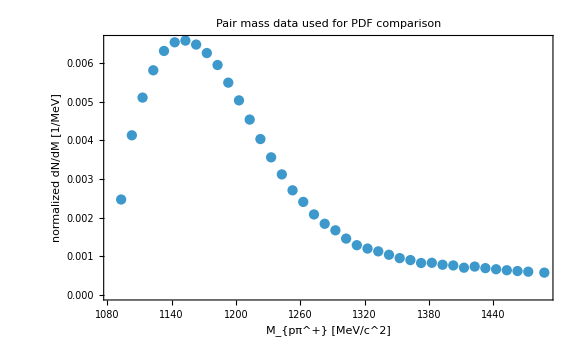

Pair curve diagnostic table in fit window:

Model | fit-window curve points | min y | max y | first curve points
BreitWigner | 301 | 6.45127×10^-4 | 6.7075×10^-3 | {{1100.,0.00437275},{1101.,0.00442564},{1102.,0.00447887},{1103.,0.00453242},{1104.,0.00458625}}
Cugnon | 301 | 6.63085×10^-4 | 6.79699×10^-3 | {{1100.,0.00395933},{1101.,0.00405643},{1102.,0.00415061},{1103.,0.00424216},{1104.,0.00433133}}
PhaseShift | 301 | 6.48328×10^-4 | 6.77844×10^-3 | {{1100.,0.00409039},{1101.,0.00417321},{1102.,0.00425423},{1103.,0.0043336},{1104.,0.00441143}}

Pair curve diagnostic table in display window:

Model | display-window curve points | min y | max y | first curve points
BreitWigner | 301 | 3.39508×10^-4 | 6.70711×10^-3 | {{1080.,0.00340856},{1081.4,0.00346946},{1082.8,0.00353141},{1084.2,0.00359441},{1085.6,0.00365844}}
Cugnon | 301 | 3.52886×10^-4 | 6.79649×10^-3 | {{1080.,0.0004147},{1081.4,0.000800609},{1082.8,0.00118793},{1084.2,0.00155114},{1085.6,0.00188183}}
PhaseShift | 301 | 3.20344×10^-4 | 6.77844×10^-3 | {{1080.,0.00137768},{1081.4,0.00175455},{1082.8,0.00205531},{1084.2,0.00231082},{1085.6,0.00253553}}

Pair prediction consistency table:

Model | first fitted PDF values at data masses | comment
BreitWigner | {pairInternalPDFValueMeV[1102.84,1102.84],pairInternalPDFValueMeV[1112.84,1112.84],pairInternalPDFValueMeV[1122.84,1122.84],pairInternalPDFValueMeV[1132.84,1132.84],pairInternalPDFValueMeV[1142.84,1142.84]} | same evaluator used for plot and residuals
Cugnon | {pairInternalPDFValueMeV[1102.84,1102.84],pairInternalPDFValueMeV[1112.84,1112.84],pairInternalPDFValueMeV[1122.84,1122.84],pairInternalPDFValueMeV[1132.84,1132.84],pairInternalPDFValueMeV[1142.84,1142.84]} | same evaluator used for plot and residuals
PhaseShift | {pairInternalPDFValueMeV[1102.84,1102.84],pairInternalPDFValueMeV[1112.84,1112.84],pairInternalPDFValueMeV[1122.84,1122.84],pairInternalPDFValueMeV[1132.84,1132.84],pairInternalPDFValueMeV[1142.84,1142.84]} | same evaluator used for plot and residuals

Pair fit plot:

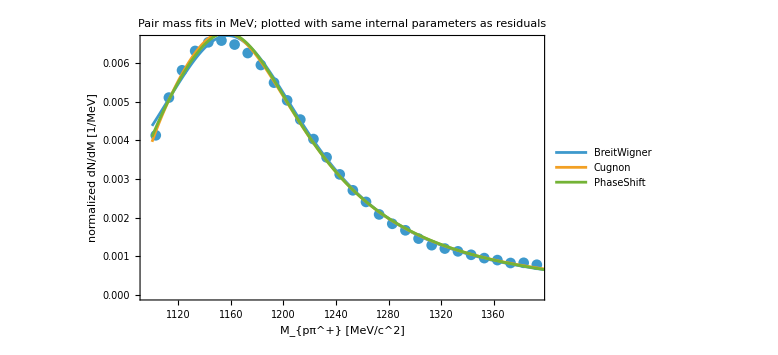

Pair fit plot on data-scale y range:

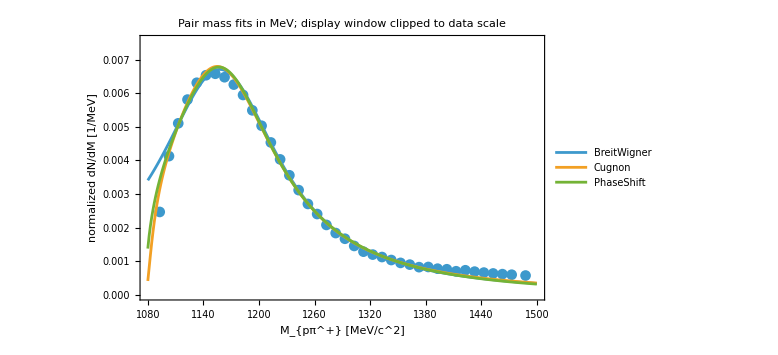

Pair fit residual plot:

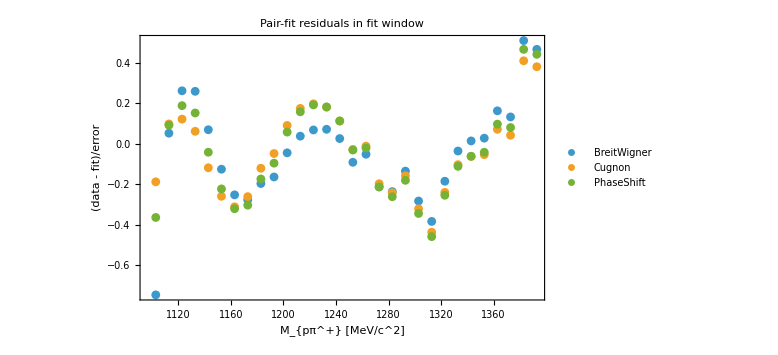

```mathematica
(* ============================================================ *)
(* 8. PLOTS - NUMERICALLY SAMPLED CURVES                        *)
(* ============================================================ *)

(* IMPORTANT:
   The numerical fit is performed with the internal parameter vector stored in
      pairFitResultsMeV[name]["BestFitParametersMeVFit"] .
   For PhaseShift this vector contains c1u and c2u, i.e. the variables actually
   used by NMinimize.  The registered/output parameters contain physical c1,c2.

   Therefore the plot must never reconstruct the PhaseShift curve from
   pairFittedMassParameters or pairFittedMassParametersMeVDisplay.  It must use
   exactly the same internal fitted parameters and exactly the same raw model as
   chi2 and residuals.  This block makes that explicit. *)

ClearAll[
  pairInternalParameterVectorMeV,
  pairInternalRawModelMeV,
  pairInternalNormMeV,
  pairInternalPDFValueMeV,
  pairModelCurveDataMeV,
  pairCurveDiagnosticGrid,
  pairResidualData,
  pairPredictionConsistencyTable
];

pairInternalParameterVectorMeV[name_String] := Module[{res, parNames, parsAssoc},
  If[! KeyExistsQ[pairFitResultsMeV, name], Return[Missing["NoModel"]]];
  res = pairFitResultsMeV[name];
  If[res["Status"] =!= "OK", Return[Missing["NoSuccessfulFit"]]];
  parNames = res["ParameterNames"];
  parsAssoc = res["BestFitParametersMeVFit"];
  Lookup[parsAssoc, parNames]
];

pairInternalRawModelMeV[name_String] := Module[{res},
  If[! KeyExistsQ[pairFitResultsMeV, name], Return[Missing["NoModel"]]];
  res = pairFitResultsMeV[name];
  If[! KeyExistsQ[res, "ModelFunction"], Return[Missing["NoModelFunction"]]];
  res["ModelFunction"]
];

pairInternalNormMeV[name_String] := pairInternalNormMeV[name] = Module[{model, pars, norm},
  model = pairInternalRawModelMeV[name];
  pars = pairInternalParameterVectorMeV[name];
  If[! ListQ[pars] || MissingQ[model], Return[Indeterminate]];
  norm = Quiet @ Check[pairShapeNormMeV[model, pars], Indeterminate];
  If[NumericQ[norm] && norm > 0, norm, Indeterminate]
];

pairInternalPDFValueMeV[name_String, mass_?NumericQ] := Module[{model, pars, norm, raw, val},
  model = pairInternalRawModelMeV[name];
  pars = pairInternalParameterVectorMeV[name];
  norm = pairInternalNormMeV[name];
  If[MissingQ[model] || ! ListQ[pars] || ! NumericQ[norm] || norm <= 0, Return[Indeterminate]];
  raw = Quiet @ Check[model[N[mass], Sequence @@ pars], Indeterminate];
  val = raw/norm;
  If[NumericQ[val] && FreeQ[val, Indeterminate | ComplexInfinity | DirectedInfinity[_]], N[val], Indeterminate]
];

pairFitCurveMassGridMeV = N @ Subdivide[pairFitMassWindowMeV[[1]], pairFitMassWindowMeV[[2]], 300];
pairDisplayCurveMassGridMeV = N @ Subdivide[pairDisplayMassWindowMeV[[1]], pairDisplayMassWindowMeV[[2]], 300];

pairModelCurveDataMeV[name_String, grid_List] := Module[{vals},
  vals = ({#, pairInternalPDFValueMeV[name, #]} & /@ grid);
  Select[vals, VectorQ[#, NumericQ] && FreeQ[#, Indeterminate | ComplexInfinity | DirectedInfinity[_]] &]
];

(* Curve sampling is deliberately sequential.  The fit itself may be parallel,
   but curves are cheap and should not depend on stale subkernel definitions. *)
pairModelCurveAssociationFitMeV = AssociationMap[pairModelCurveDataMeV[#, pairFitCurveMassGridMeV] &, Keys[pairModelSpecs]];
pairModelCurveAssociationFitMeV = Select[pairModelCurveAssociationFitMeV, Length[#] > 5 &];

pairModelCurveAssociationDisplayMeV = AssociationMap[pairModelCurveDataMeV[#, pairDisplayCurveMassGridMeV] &, Keys[pairModelSpecs]];
pairModelCurveAssociationDisplayMeV = Select[pairModelCurveAssociationDisplayMeV, Length[#] > 5 &];

pairModelCurveAssociationMeV = pairModelCurveAssociationFitMeV;
pairModelCurveDataMeV[name_String] := Lookup[pairModelCurveAssociationFitMeV, name, {}];

pairCurveDiagnosticGrid[assoc_Association, title_String] := Grid[
  Prepend[
    KeyValueMap[
      {#1, Length[#2], If[Length[#2] > 0, ScientificForm[Min[#2[[All, 2]]], {10, 5}], Missing["NoCurve"]],
       If[Length[#2] > 0, ScientificForm[Max[#2[[All, 2]]], {10, 5}], Missing["NoCurve"]],
       If[Length[#2] > 0, Take[#2, UpTo[5]], Missing["NoCurve"]]} &,
      assoc
    ],
    {"Model", title <> " curve points", "min y", "max y", "first curve points"}
  ],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairCurveDiagnosticTable = pairCurveDiagnosticGrid[pairModelCurveAssociationFitMeV, "fit-window"];
pairDisplayCurveDiagnosticTable = pairCurveDiagnosticGrid[pairModelCurveAssociationDisplayMeV, "display-window"];

pairPredictionConsistencyTable = Grid[
  Prepend[
    KeyValueMap[
      Module[{masses, curveVals},
        masses = Take[pairMassValsMeV, UpTo[5]];
        curveVals = pairInternalPDFValueMeV[#1, #] & /@ masses;
        {#1, curveVals, "same evaluator used for plot and residuals"}
      ] &,
      Select[pairFitResultsMeV, #Status === "OK" &]
    ],
    {"Model", "first fitted PDF values at data masses", "comment"}
  ],
  Frame -> All, Background -> {LightGray, None}, Alignment -> Left
];

pairSelectedDataPlot = ListPlot[
  pairDisplayDataPDFMeV,
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"M_{pπ^+} [MeV/c^2]", "normalized dN/dM [1/MeV]"},
  PlotLabel -> "Pair mass data used for PDF comparison",
  PlotRange -> All,
  ImageSize -> Large
];

pairFitDataPlot = ListPlot[
  Transpose[{pairMassValsMeV, pairYValsPDFMeV}],
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"M_{pπ^+} [MeV/c^2]", "normalized dN/dM [1/MeV]"},
  PlotLabel -> "Pair mass data in fit window",
  PlotRange -> All,
  ImageSize -> Large
];

pairFitPlot = If[Length[pairModelCurveAssociationFitMeV] > 0,
  Show[
    ListPlot[
      Transpose[{pairMassValsMeV, pairYValsPDFMeV}],
      PlotMarkers -> Automatic,
      PlotRange -> All
    ],
    ListLinePlot[
      Values[pairModelCurveAssociationFitMeV],
      PlotLegends -> Keys[pairModelCurveAssociationFitMeV],
      PlotRange -> All
    ],
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"M_{pπ^+} [MeV/c^2]", "normalized dN/dM [1/MeV]"},
    PlotLabel -> "Pair mass fits in MeV; plotted with same internal parameters as residuals",
    ImageSize -> Large
  ],
  Style["No successful pair-fit curves to plot.", Red]
];

pairDataYMaxMeV = Max[pairDisplayDataPDFMeV[[All, 2]]];
pairFitPlotDataScale = If[Length[pairModelCurveAssociationDisplayMeV] > 0,
  Show[
    ListPlot[
      pairDisplayDataPDFMeV,
      PlotMarkers -> Automatic,
      PlotRange -> {{pairDisplayMassWindowMeV[[1]], pairDisplayMassWindowMeV[[2]]}, {0, 1.15 pairDataYMaxMeV}}
    ],
    ListLinePlot[
      Values[pairModelCurveAssociationDisplayMeV],
      PlotLegends -> Keys[pairModelCurveAssociationDisplayMeV],
      PlotRange -> {{pairDisplayMassWindowMeV[[1]], pairDisplayMassWindowMeV[[2]]}, {0, 1.15 pairDataYMaxMeV}}
    ],
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"M_{pπ^+} [MeV/c^2]", "normalized dN/dM [1/MeV]"},
    PlotLabel -> "Pair mass fits in MeV; display window clipped to data scale",
    ImageSize -> Large
  ],
  Style["No successful pair-fit curves to plot.", Red]
];

pairResidualData[name_String] := Module[{},
  If[! KeyExistsQ[pairFitResultsMeV, name] || pairFitResultsMeV[name]["Status"] =!= "OK", Return[{}]];
  MapThread[
    {#1, (#2 - pairInternalPDFValueMeV[name, #1])/#3} &,
    {pairMassValsMeV, pairYValsPDFMeV, pairErrorValsPDFMeV}
  ]
];

pairFitResidualPlot = ListPlot[
  AssociationMap[pairResidualData, Keys[pairModelSpecs]],
  Frame -> True,
  Axes -> False,
  FrameLabel -> {"M_{pπ^+} [MeV/c^2]", "(data - fit)/error"},
  PlotLabel -> "Pair-fit residuals in fit window",
  PlotLegends -> Keys[pairModelSpecs],
  PlotRange -> All,
  ImageSize -> Large
];

Print["Pair selected data plot:"];
Print[pairSelectedDataPlot];
Print["Pair curve diagnostic table in fit window:"];
Print[pairCurveDiagnosticTable];
Print["Pair curve diagnostic table in display window:"];
Print[pairDisplayCurveDiagnosticTable];
Print["Pair prediction consistency table:"];
Print[pairPredictionConsistencyTable];
Print["Pair fit plot:"];
Print[pairFitPlot];
Print["Pair fit plot on data-scale y range:"];
Print[pairFitPlotDataScale];
Print["Pair fit residual plot:"];
Print[pairFitResidualPlot];
```

```mathematica
(* ============================================================ *)
(* 9. COMPATIBILITY ALIASES                                      *)
(* ============================================================ *)

pairFitWindow = pairFitMassWindowMeV;
pairFitNormalizationWindow = pairNormalizationWindowMeV;
pairFitDisplayWindow = pairDisplayMassWindowMeV;

pairFittedModels = pairFitResultsMeV;
pairFittedParameters = pairFittedMassParameters;
pairFittedParametersMeV = pairFittedMassParameters;
pairFittedParametersMeVFit = pairFittedMassParametersMeVFit;
massParameterSummary[]

Print["PairFit finished. Fits were performed in MeV; registered Fitted parameters are in MeV and ready for setAnalysisMode[\"Fitted\"]."];
```

Model | Vacuum parameters | Fitted parameters
BreitWigner | <|M0→1232.,Gamma0→117.|> | <|M0→1157.75,Gamma0→158.052|>
Cugnon | <|M0→1232.,Gamma0→117.,mu→180.|> | <|M0→1152.85,Gamma0→160.031,mu→46.3694|>
PhaseShift | <|M0→1232.,alpha0→45.37,c1→0.0000167,c2→6.56×10^-11|> | <|M0→1187.3,alpha0→179.142,c1→0.0000654242,c2→7.9735×10^-10|>

PairFit finished. Fits were performed in MeV; registered Fitted parameters are in MeV and ready for setAnalysisMode["Fitted"].